```mathematica
ParametricPlot3D[{Cos[θ]Cos[ϕ],Sin[θ]Cos[ϕ],Sin[ϕ]},{θ,-4,4},{ϕ,-4,4}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t,t^2,t^3},{t,-20,20},PlotRange-> {{-5,5},{-5,5},{-5,5}},PlotPoints->100]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x*t,x*t^2,x*t^3},{t,-20,20},{x,-10,10},PlotRange-> {{-5,5},{-5,5},{-5,5}},PlotPoints->300]
```

-Graphics3D-

```mathematica
ContourPlot3D[{y*y==x*z},{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

```mathematica
Eigenvalues[{{0,0,1/2},{0,-1,0},{1/2,0,0}}]
```

{-1,-1/2,1/2}

```mathematica
ParametricPlot3D[{r*(1+Sin[θ]),r*Cos[θ],r*(1-Sin[θ])},{r,-20,20},{θ,-10,10},PlotRange-> {{-5,5},{-5,5},{-5,5}}]
```

-Graphics3D-

```mathematica
Plot3D[x^2-y^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{x^2-y^2,2x-2y},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[x^2+y^2],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[x^2+y^2],x/Sqrt[2]-y/Sqrt[2]},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[x*y/(x^2+y^2),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[(x^2*y)/(x^6+y^2),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
D[{(x^2*y)/(x^2+y^2)},x]
D[{(x^2*y)/(x^2+y^2)},y]
```

{-(2 x^3 y)/((x^2+y^2)^2)+(2 x y)/(x^2+y^2)}

{-(2 x^2 y^2)/((x^2+y^2)^2)+x^2/(x^2+y^2)}

```mathematica
Plot3D[(x^2*y)/(x^2+y^2),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
D[{x*y,x^2-y^2},y]
```

{x,-2 y}

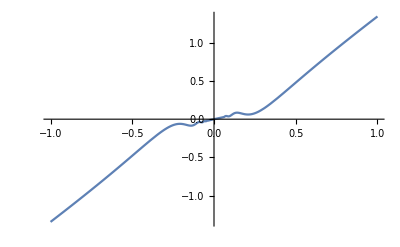

```mathematica
Plot[x/2+x^2*Sin[1/x],{x,-1,1}]
```

```mathematica
D[x/2+(x^2*Sin[1/x]),{x,0}]
```

x/2+x^2 Sin[1/x]

```mathematica
Limit[h*Sin[1/h],h->0]
```

0

```mathematica
D[{(x/2)+(x^2*Sin[1/x])},x]
```

{1/2-Cos[1/x]+2 x Sin[1/x]}

```mathematica
f[x_,y_]=ϕ[(x+y)/(x-y)];
D[f[x,y],x]
```

(2 (x+y))/(x-y)^2-(2 (x+y)^2)/(x-y)^3

```mathematica
x*(D[(x+y)/(x-y),x])+y*(D[(x+y)/(x-y),y])
```

x (1/(x-y)-(x+y)/(x-y)^2)+y (1/(x-y)+(x+y)/(x-y)^2)

```mathematica
y*(D[(x+y)/(x-y),y])
```

y (1/(x-y)+(x+y)/(x-y)^2)

```mathematica
D[x/y,y]
```

-x/y^2

```mathematica
D[x/2+x^2*Sin[1/x],x]
```

1/2-Cos[1/x]+2 x Sin[1/x]

Power::infy: Infinite expression 1/0 encountered.

Indeterminate

```mathematica
Limit[(h/2+h^2*Sin[1/h])/h,h->0]
```

1/2

```mathematica
D[{x*y,x^2-y^2},x]
```

{y,2 x}

```mathematica
D[{x*y,x^2-y^2},y]
```

{x,-2 y}

```mathematica
Series
```